```mathematica
Remove["Global`*"];
(*SetDirectory["..."]*)(*descomentar y poner un directorio donde se guardaran los pdfs*)
```

# Example 1: Adding mutation

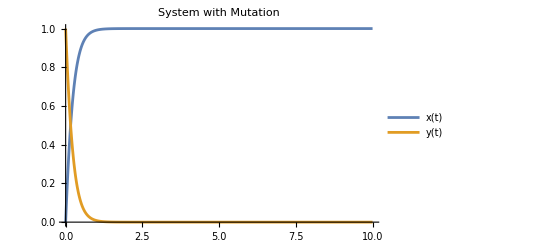

```mathematica
a=2;b=1;(*fitness value*)
mab = 0; mba=4;
phi[t_]:=a*x[t]+b*y[t]; (*average fitness*)
eq1=(x'[t]==(a-phi[t]-mab)*x[t]+mba*y[t]); (*the three equations*)
eq2=(y'[t]==(b-phi[t]-mba)*y[t]+mab*x[t]);
initialConditions={x[0]==0,y[0]==1}; (*initial conditions*)
solution=NDSolve[{eq1,eq2,initialConditions},{x[t],y[t]},{t,0,100}]; (*function to solve the equation*)
{xSol,ySol}={x[t],y[t]}/. solution[[1]]; (*extract the solutions*)
PlotODE4=Plot[{xSol,ySol},{t,0,10},PlotLegends->{"x(t)","y(t)"},FrameLabel->{"t","Values"},PlotLabel->"System with Mutation"] (*plot*)
```

```mathematica
(*Export["grafico_ode4.pdf",PlotODE4]*)
```

# Example 2: SIR model

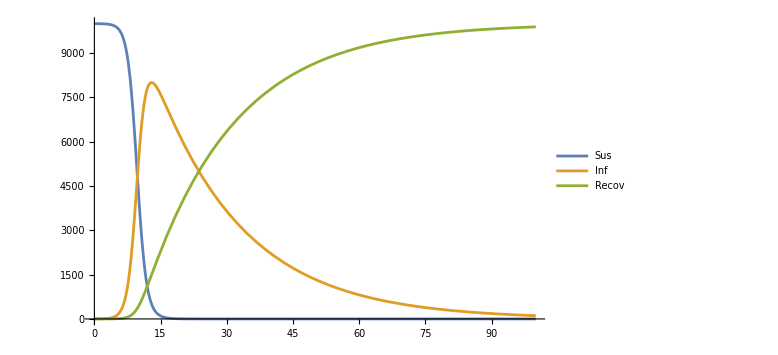

```mathematica
(*SIR*)
ClearAll[Sus,Inf,Recov,a,b,tmax,g,x,y] (*remove previous variables .. just in case*)

tmax=200;

soln=First@NDSolve[{Sus'[t]==(-b)*Sus[t]*Inf[t]/No,Inf'[t]==b*Sus[t]*Inf[t]/No-g*Inf[t],Recov'[t]==g*Inf[t],Sus[0]==No-1,Inf[0]==1,Recov[0]==0,b==1,g==0.05,No==10000},{Sus,Inf,Recov},{t,0,tmax}];

PPSIR1=Plot[{Sus[t]/. soln,Inf[t]/. soln,Recov[t]/. soln},{t,0,100},PlotRange->All,PlotLegends->{"Sus","Inf","Recov"},ImageSize->Large]
(*Export["grafico_SIR1.pdf",PPSIR1];*)
```

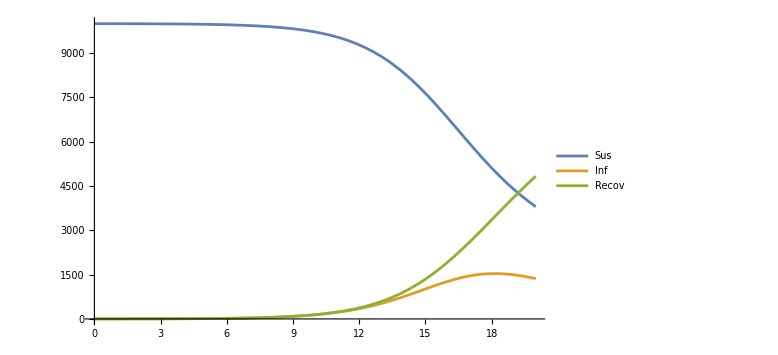

```mathematica
(*SIR*)
ClearAll[Sus,Inf,Recov,a,b,tmax,g];
tmax=20;
soln=First@NDSolve[{Sus'[t]==(-b)*Sus[t]*Inf[t]/No,Inf'[t]==b*Sus[t]*Inf[t]/No-g*Inf[t],Recov'[t]==g*Inf[t],Sus[0]==No-1,Inf[0]==1,Recov[0]==0,b==1,g==0.5,No==10000},{Sus,Inf,Recov},{t,0,tmax}];

PPSIR1=Plot[{Sus[t]/. soln,Inf[t]/. soln,Recov[t]/. soln},{t,0,tmax},PlotRange->All,PlotLegends->{"Sus","Inf","Recov"},ImageSize->Large]
(*Export["grafico_SIR2.pdf",PPSIR1]*)
```

## Example 2.1: SIR model without fixed size. Here susceptible reproduce at rate a, so the total number of individuals in the population is increasing

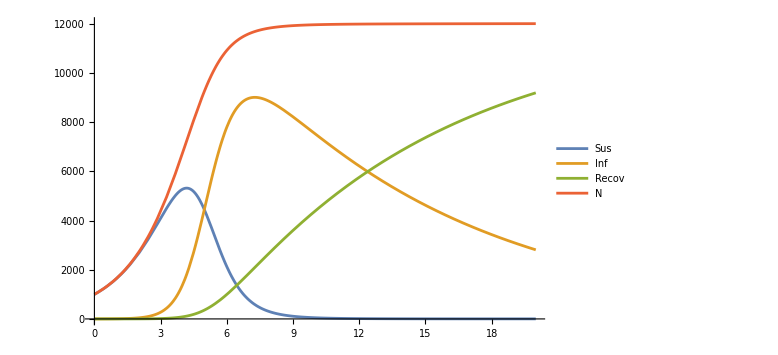

```mathematica
ClearAll[Sus,Inf,Recov,a,b,tmax,g,No];
tmax=20;
a=0.5;b=2;g=0.1;
No[t_]:=Sus[t]+Inf[t]+Recov[t]

soln=First@NDSolve[{Sus'[t]==(-b)*Sus[t]*Inf[t]/No[t]+a*Sus[t],Inf'[t]==b*Sus[t]*Inf[t]/No[t]-g*Inf[t],Recov'[t]==g*Inf[t],Sus[0]==1000-1,Inf[0]==1,Recov[0]==0},{Sus,Inf,Recov},{t,0,tmax}];

PPSIR1=Plot[{Sus[t]/. soln,Inf[t]/. soln,Recov[t]/. soln, No[t]/.soln},{t,0,tmax},PlotRange->All,PlotLegends->{"Sus","Inf","Recov", "N"},ImageSize->Large]
(*Export["grafico_SIR3.pdf",PPSIR1]*)
```